```mathematica
f[r_,z_,t_,v_]:=-v (z-v t)/((z-v t)^2 + (1-v^2)r^2 )^(3/2)
F[r_,z_,t_,v_]:=Piecewise[{{f[r,z,t,v],t>=Sqrt[r^2 + z^2]}},0]
```

```mathematica
g[r_,z_,t_,v_,M_]:=1-2/(1+Exp[M*f[r,z,t,v]]);
G[r_,z_,t_,v_,N_,M_]:=Piecewise[{{g[r,z,t,v,M],t>=Sqrt[r^2 + z^2]},{g[(t-0.1) r/Sqrt[r^2+z^2] ,(t-0.1)z/Sqrt[r^2+z^2],t,v,M]/(1+Exp[N*(Sqrt[r^2+z^2]-t-1)]),t<Sqrt[r^2+z^2]}}];
t=10;
v=1.5;
L=10;
pp=20;
e[x_,a_]:=Exp[a(Abs[x]-1)]
plot =DensityPlot3D[G[Sqrt[x^2+y^2],z,t,v,4,2],{x,-L,L},{y,-L,L},{z,-0.1L,1.9L},PlotTheme->"Thermal",Axes->False,Background->None,PlotPoints->pp,ColorFunction->Function[{z},ColorData["TemperatureMap"][(z+1)/2]],ColorFunctionScaling->False,ImageSize->Large,OpacityFunctionScaling->False,OpacityFunction->Function[{z},e[z,5]],ViewPoint->{1.3,-2.4,2.}]
```

-Graphics3D-

```mathematica
frame[t_,pp_]:=DensityPlot3D[G[Sqrt[x^2+y^2],z,t,v,4,1],{x,-L,L},{y,-L,L},{z,-0.1L,1.9L},PlotTheme->"Ther Spemal",Axes->False,Background->None,PlotPoints->pp,ColorFunction->Function[{z},ColorData["TemperatureMap"][(z+1)/2]],ColorFunctionScaling->False,OpacityFunctionScaling->False,OpacityFunction->Function[{z},e[z,5]],ImageSize->Large,ViewPoint->{1.3,-2.4,2.}]

(*m =Animate[frame[t],{t,0.01,20,0.1}]*)
```

```mathematica
ProgressIndicator[Dynamic[n],{0.01,20}]
frames = Table[(n=t;frame[t,100]),{t,0.01,20,0.5}];
```

```mathematica
Export["/Users/panos/Desktop/mid_res_fast.mp4",frames];
```

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[#~StringDrop~1~FromDigits~16,256,3]/255.)&;
```

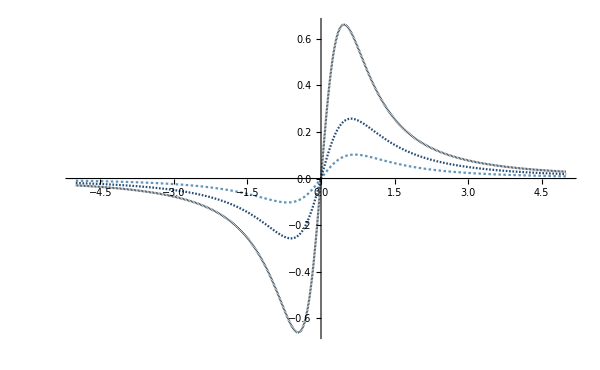

```mathematica
r = 1;
L = 5;
t=100;
v={0.25,0.5,0.75};
Colors={"#6096BA","#274C77","#112634"};
LS=Table[Dashing[r,0.01-r],{r,{0.003,0.002,0.0001}}];
n=3;
Plots = MapThread[Plot[-F[r,z+#1 t,t,#1],{z,-L,+L},PlotRange->All,PlotStyle->{hexToRGB[#2],#3}]&,{v,Colors,LS}];
Show[Plots,PlotPoints->31,MaxRecursion->8,PlotRange->All,
FrameLabel->{"z-vt","Pressure"},
AxesStyle->Arrowheads[{0,0.015}],
GridLines->None]
```

```mathematica
arrowheadNames=GraphElementData["Edge"];
```